```mathematica
(*https://openstax.org/books/university-physics-volume-3/pages/7-6-the-quantum-tunneling-of-particles-through-potential-barriers*)
Clear["Global`*"]
NotebookSave[]
(*https://mathematica.stackexchange.com/questions/38114/how-to-set-the-working-precision-globally-minprecision-does-not-work*)
(*$PreRead=(#/. s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`20."&);*)
SetOptions[SelectedNotebook[],PrintPrecision->20]
```

```mathematica
eq = psi''[x] + 2.*mass/(HBAR^2)*psi[x]*(energy - workFunction + x*bias/w)==0
```

(2. mass (energy-workFunction+(bias x)/w) psi[x])/HBAR^2+psi''[x]==0

Solving the equation without constraints

```mathematica
DSolve[psi''[x] + 2.*mass/(HBAR^2)*psi[x]*(energy- workFunction + x*bias/w)==0, psi[x], x] // Simplify
```

{{psi[x]→AiryAi[(1.25992 (-(bias mass)/(HBAR^2 w))^(1/3) (1. energy w-1. w workFunction+1. bias x))/bias] C[1]+AiryBi[(1.25992 (-(bias mass)/(HBAR^2 w))^(1/3) (1. energy w-1. w workFunction+1. bias x))/bias] C[2]}}

```mathematica
vals = {mass-> 9.1093837*10^(-31), HBAR->1.054571817*10^(-34)/(2*Pi),  energy-> 2.5*1.60217663*10^(-19), workFunction->5* 1.60217663*10^(-19), bias->0.3*1.60217663*10^(-19)}
```

{mass→9.10938×10^-31,HBAR→1.6784×10^-35,energy→4.00544×10^-19,workFunction→8.01088×10^-19,bias→4.80653×10^-20}

Displaying the Airy functions

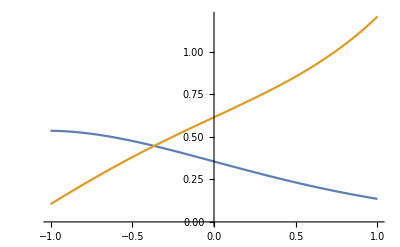

```mathematica
Plot[{Re[AiryAi[x]],Re[AiryBi[x]]}, {x,-1,1}]
```

Determining symbolic expressions of the reflectance and transmittance coefficients.

```mathematica
simEq = {r*(K11 + I*k1) + t*K12*Exp[I*k3*w] + K11 - I*k1 == 0, r*K21 + t*(K22 - I*k3)*Exp[I*k3*w] + K21 == 0}
```

{-ⅈ k1+K11+(ⅈ k1+K11) r+ⅇ^(ⅈ k3 w) K12 t==0,K21+K21 r+ⅇ^(ⅈ k3 w) (K22-ⅈ k3) t==0}

```mathematica
Timing[mSol = Solve[simEq, {r,t}] // Simplify]
ComplexExpand[ReIm[-(K12 K21+(k1+ⅈ K11) (ⅈ K22+k3))/(K12 K21-(k1-ⅈ K11) (ⅈ K22+k3))]]
ComplexExpand[ReIm[(2 k1 K21)/(-ⅈ  K12 K21+ (ⅈ k1+K11) (ⅈ K22+k3))]]
```

{0.015625,{{r→(-ⅈ K12 K21+(k1+ⅈ K11) (K22-ⅈ k3))/(ⅈ K12 K21+(k1-ⅈ K11) (K22-ⅈ k3)),t→-(2 ⅇ^(-ⅈ k3 w) k1 K21)/(ⅈ K12 K21+(k1-ⅈ K11) (K22-ⅈ k3))}}}

{-(K12^2 K21^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 K11 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2),-(2 k1 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)}

{-(2 k1^2 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2),(2 k1 K12 K21^2)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1 K11 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1^2 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)}

Generating the kappa matrix

```mathematica
w =.
zeta = -(2.*bias*mass/(w*HBAR^2))^(1./3.)
alpha[x_] := (zeta(energy *w-w *workFunction+bias*x))/bias
kappa = zeta*{{AiryAiPrime[alpha[0]]*AiryBi[alpha[w]] - AiryAi[alpha[w]]*AiryBiPrime[alpha[0]], AiryAi[alpha[0]]*AiryBiPrime[alpha[0]] - AiryAiPrime[alpha[0]]*AiryBi[alpha[0]]}, {AiryAiPrime[alpha[w]]*AiryBi[alpha[w]] - AiryAi[alpha[w]]*AiryBiPrime[alpha[w]], AiryAi[alpha[0]]*AiryBiPrime[alpha[w]] - AiryAiPrime[alpha[w]]*AiryBi[alpha[0]]} }/ (AiryAi[alpha[0]]*AiryBi[alpha[w]] - AiryAi[alpha[w]]*AiryBi[alpha[0]]);
```

-1.25992 ((bias mass)/(HBAR^2 w))^0.333333

```mathematica
kappaSub = {K11->kappa[[1,1]], K12->kappa[[1,2]], K21->kappa[[2,1]], K22->kappa[[2,2]]};
```

```mathematica
wavenumbers = {k1 -> Sqrt[2.*mass*energy]/HBAR, k3 -> Sqrt[2.*mass*(energy + bias)]/HBAR}
```

{k1→(1.41421 √(energy mass))/HBAR,k3→(1.41421 √((bias+energy) mass))/HBAR}

```mathematica
{(AiryAi[alpha[0]]*AiryBi[alpha[w]] - AiryAi[alpha[w]]*AiryBi[alpha[0]]), alpha[w]} /. w->5.*^-10 /. vals /. wavenumbers
```

{-1.42462×10^9,31.2945}

Creating the transmittance coefficient as a function of width (w).

```mathematica
refCoff = (-(K12^2 K21^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 K11 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))^2 + (-(2 k1 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))^2;
transCoff = (-((2 k1^2 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2))+(2 k1 K11 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2))^2 + ((2 k1 K12 K21^2)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1 K11 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1^2 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2))^2;
Timing[trans[w_] = transCoff / (refCoff + transCoff) /. kappaSub // Refine]
```

```mathematica
transVals[w_] = Evaluate[trans[w] /. wavenumbers /.vals ];
```

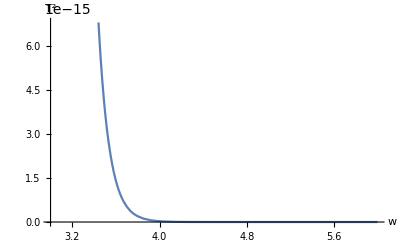

```mathematica
Plot[transVals[w], {w,3.*^-10,6.*^-10}, AxesLabel->{"w", T^2}]
```

```mathematica
{refCoff, transCoff} /. kappaSub /. wavenumbers /.vals /. w->5.*^-10
trans[5.*^-10] /. wavenumbers /.vals
```

{1.,1.40373×10^-21}

1.40373×10^-21

Creating the transmittance derivative

```mathematica
w=.
Timing[dtrans[w_] = D[trans[w], w];]
Taim = 0.0014592199657413873;
```

{0.03125,Null}

Newton-Raphson

```mathematica
dtransVals[w_] = dtrans[w] /. wavenumbers /.vals ;
Timing[
x = 1.*^-10;
For[i = 0, i < 10, i+=1, 
x = x - (transVals[x]- Taim)/ dtransVals[x]]]
Print[x]
```

{0.171875,Null}

7.95775×10^-11

Set global assumptions.

```mathematica
$Assumptions = {Element[mass,Reals], Element[energy,Reals], Element[bias,Reals], Element[workFunction,Reals], Element[HBAR,Reals], Element[w,Reals], Element[k1,Reals], Element[k3,Reals], mass>0, energy>0, bias>0, workFunction>0, HBAR>0, w>0, k1>0, k3>0}
```

{mass∈ℝ,energy∈ℝ,bias∈ℝ,workFunction∈ℝ,HBAR∈ℝ,w∈ℝ,k1∈ℝ,k3∈ℝ,mass>0,energy>0,bias>0,workFunction>0,HBAR>0,w>0,k1>0,k3>0}

Generate expressions for the weighting coefficients.

```mathematica
matinv= Inverse[{{AiryAi[alpha[0]], AiryBi[alpha[0]]},{AiryAi[alpha[w]], AiryBi[alpha[w]]}}];
vec =  {1 -(K12*K21 + I*k1*K22 - K11*K22 + k1*k3 + I*K11*k3 )/(K12*K21 - I*k1*K22 - K11*K22 - k1*k3 + I*K11*k3), - ((2*k1*kappa[[2,1]])/(I*kappa[[1,2]]*kappa[[2,1]]-(I*k1+kappa[[1,1]])*(I*kappa[[2,2]]+k3)))};(*{1 -(kappa[[1,2]]*kappa[[2,1]] + I*k1*kappa[[2,2]] - kappa[[1,1]]*kappa[[2,2]] + k1*k3 + I*kappa[[1,1]]*k3 )/(kappa[[1,2]]*kappa[[2,1]] - I*k1*kappa[[2,2]] - kappa[[1,1]]*kappa[[2,2]] - k1*k3 + I*kappa[[1,1]]*k3), - (2*k1*kappa[[2,1]])/(I*kappa[[1,2]]*kappa[[2,1]]-(I*k1+kappa[[1,1]])*(I*kappa[[2,2]]+k3))}*);
vecbar = {1 + (-(K12^2 K21^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 K11 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2) - I*(-((2 k1 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))+(2 k1 K11 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))), -(2 k1^2 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2) -I*((2 k1 K12 K21^2)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1 K11 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1^2 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2))} ;
```

```mathematica
coefficients= matinv.vec;
coefficientsbar = matinv.vecbar;
```

Need to manually write the expressions due to errors with Mathematica generated expressions.

```mathematica
coff1 = coefficients[[1]];
coff2 = coefficients[[2]];
coff1bar = coefficientsbar[[1]];
coff2bar = coefficientsbar[[2]];

coff1 /. wavenumbers  /. kappaSub/. vals /. w->4.*^-10
coff2 /. wavenumbers  /. kappaSub/. vals /. w->4.*^-10
coff1bar /. wavenumbers  /. kappaSub/. vals /. w->4.*^-10
coff2bar/. wavenumbers  /. kappaSub/. vals /. w->4.*^-10

v12 = ComplexExpand[Re[vec[[1]]*vecbar[[2]]]];
v21 = (1 -(K12^2 K21^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 K11 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))*-(2 k1^2 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2) + (-((2 k1 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))+(2 k1 K11 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))*((2 k1 K12 K21^2)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1 K11 K21 K22)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2)-(2 k1^2 K21 k3)/((-K12 K21+K11 K22+k1 k3)^2+(-k1 K22+K11 k3)^2));
v11 = (1 + (-((K12^2 K21^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))+(2 K11 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(k1^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)-(K11^2 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)))^2 + (-((2 k1 K12 K21 K22)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))+(2 k1 K11 K22^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2)+(2 k1 K11 k3^2)/((K12 K21-K11 K22-k1 k3)^2+(-k1 K22+K11 k3)^2))^2;
v22 = transCoff;

c[i_,j_] := (matinv[[i,1]]*matinv[[j,1]]*v11 + matinv[[i,2]]*matinv[[j,1]]*v21 + matinv[[i,1]]*matinv[[j,2]]*v12+matinv[[i,2]]*matinv[[j,2]]*v22)

{v11,v22, v12,v21,
c[1,1],c[1,2],c[2,1],c[2,2]} /. wavenumbers /. kappaSub /. vals /. w->5.*^-10
```

6.92234×10^32+8.83952×10^32 ⅈ

3.16472×10^-49-3.16004×10^-49 ⅈ

6.92234×10^32-8.83952×10^32 ⅈ

3.16472×10^-49+3.16004×10^-49 ⅈ

{2.00237,1.40373×10^-21,3.51954×10^-11,3.5172×10^-11,1.32553×10^82,-3.38069×10^-21,-3.36425×10^-21,5.93248×10^-122}

Generate the expression for the wavefunction probability in the barrier.

```mathematica
Timing[integrand[t_] = (c[1,1] * AiryAi[alpha[t]]^2 + c[2,2]* AiryBi[alpha[t]]^2 + c[1,2] * AiryAi[alpha[t]]*AiryBi[alpha[t]] + c[2,1]* AiryAi[alpha[t]]*AiryBi[alpha[t]]) /. kappaSub]
```

Alternate expression with alpha substitution.

```mathematica
testingI[a_] = (c[1,1] * AiryAi[a]^2 + c[2,2]* AiryBi[a]^2 + c[1,2] * AiryAi[a]*AiryBi[a] + c[2,1]* AiryAi[a]*AiryBi[a]) /zeta // Simplify;
```

```mathematica
zeta*testingI[{alpha[0], alpha[5.*^-10]}] /.kappaSub/. wavenumbers /. vals /. w->5.*^-10
{1+refCoff, transCoff} /. kappaSub /. wavenumbers /. vals /. w->5.*^-10
```

{2.00237,1.40373×10^-21}

{2.,1.40373×10^-21}

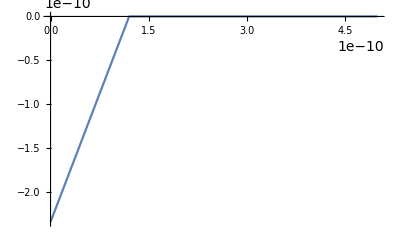
{0.25,-Graphics-}

```mathematica
Plot[{testingI[alpha[t]]}/.wavenumbers /.kappaSub /. vals /. w->5.*^-10, {t,0, 5.*^-10} ,PlotRange->Full, PlotPoints->5, MaxRecursion->0] // Timing
```

Generate expression for the area under this section of the probability density.

```mathematica
Timing[area2[w_] = Integrate[testingI[t], {t,alpha[0],alpha[w]}, Assumptions->{t ∈Reals}] /. kappaSub](*Refine[Integrate[integrand[t], {t,0,w}, Assumptions->{t>0, t ∈Reals}]]]*)
```

```mathematica
Timing[area2[{4.,5.}*10^(-10)] /. wavenumbers /. vals]
```

{0.171875,{1.97353×10^-11,1.97177×10^-11}}

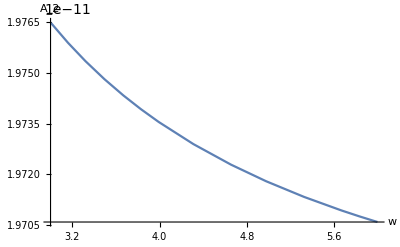
{1.,-Graphics-}

```mathematica
Timing[Plot[area2[w] /.wavenumbers /. vals, {w, 3.*^-10,6.*^-10}, PlotPoints->10,MaxRecursion->1, AxesLabel->{"w","A_2"}]]
```

```mathematica
NRf[w_] = trans[w]*(Pi / k1 + (gamma-1)*w*(1/r - 1)) - 2*Pi/k1 - area2[w]
```

```mathematica
g = 1+(Pi/k1*(2 - trans[w]) + w*area2[w]) / (w*trans[w]) /. wavenumbers /. vals /. w->4.5*^-10
```

1.40696×10^18

```mathematica
NRf[4.5*^-10] /. gamma->g /. r->0.5 /. wavenumbers /. vals
```

-1.97255×10^-11

```mathematica
Timing[Plot3D[{NRf[w] /. wavenumbers /. vals /. gamma->g, 0}, {w, 3.*^-10, 6.*^-10}, {r, 0., 1.}, ColorFunction->Hue, AxesLabel->{"w","r", "f(w,r)"}, PlotPoints->5, MaxRecursion->0]]
```

{10.4688,-Graphics3D-}

```mathematica
Timing[ContourPlot[0==NRf[w] /. wavenumbers /. vals /. gamma->g, {w, 3.*^-10, 6.*^-10}, {r, 0., 1.}, FrameLabel->{"w","r"}, PlotPoints->10,MaxRecursion->1]]
```

{12.5,-Graphics-}

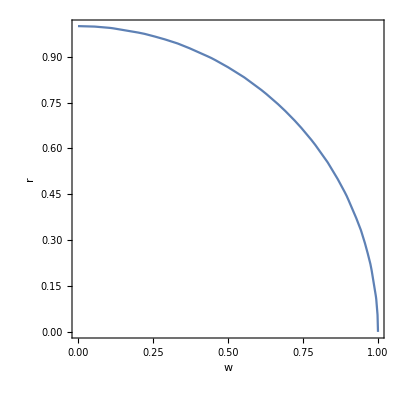
{0.015625,-Graphics-}

```mathematica
Timing[ContourPlot[1==w^2+r^2, {w, 0., 1.}, {r, 0., 1.}, FrameLabel->{"w","r"}, PlotPoints->10,MaxRecursion->1]]
```

```mathematica
dx = 1*^-20;
Timing[
x = 4.4*^-10;
For[i = 0, i < 10, i+=1, 
a=NRf[x]/. wavenumbers /. vals /. gamma->g /. r->0.4617609311166616;
x = x - a*dx/ (NRf[x+dx]-a) /. wavenumbers /. vals /. gamma->g /. r->0.4617609311166616;
Print[x]]]
Print[x]
```

4.46438×10^-10

4.4949×10^-10

4.50037×10^-10

4.50052×10^-10

4.50052×10^-10

4.50052×10^-10

«4 more identical outputs»

{2.78125,Null}

4.50052×10^-10

```mathematica
CForm[NRf[w]]
```

(-2*Pi)/k1 + ((Pi/k1 + (-1 + gamma)*(-1 + 1/r)*w)*
      (Power((3.174802103936399*k1*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
             (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias) - 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias))*
             (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias) - 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)))/
           (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (bias*w + energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias),2)*
             (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)) + 
                 (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)),2) + 
               Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2) - 
                 (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2),2))) - 
          (3.174802103936399*Power(k1,2)*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
             (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (bias*w + energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias))*
             (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias) - 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)))/
           (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (bias*w + energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias),2)*
             (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)) + 
                 (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)),2) + 
               Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2) - 
                 (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2),2))),2) + 
        Power((2.5198420997897464*Power(k1,2)*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
             (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias) - 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)))/
           ((-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (bias*w + energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias))*
             (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)) + 
                 (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)),2) + 
               Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2) - 
                 (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2),2))) + 
          (4.*k1*Power((bias*mass)/(Power(HBAR,2)*w),1.)*
             (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias) - 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias))*
             (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (bias*w + energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias))*
             (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias) - 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)))/
           (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (bias*w + energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias),3)*
             (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)) + 
                 (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)),2) + 
               Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2) - 
                 (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2),2))) - 
          (4.*k1*Power((bias*mass)/(Power(HBAR,2)*w),1.)*
             (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias))*
             Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias) - 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias),2))/
           (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (bias*w + energy*w - w*workFunction))/bias)*
                  AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                      (energy*w - w*workFunction))/bias)) + 
               AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias),3)*
             (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)) + 
                 (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)),2) + 
               Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (bias*w + energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2) - 
                 (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                    (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)*
                         AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                             (energy*w - w*workFunction))/bias)) + 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias))*
                    (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias) - 
                      AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)))/
                  Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias),2),2))),2)))/
    (Power((3.174802103936399*k1*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias))*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) - 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) - 
        (3.174802103936399*Power(k1,2)*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
           (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias))*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) - 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))),2) + 
      Power((2.5198420997897464*Power(k1,2)*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)))/
         ((-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias))*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) - 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) + 
        (4.*k1*Power((bias*mass)/(Power(HBAR,2)*w),1.)*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias))*
           (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias))*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),3)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) - 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) - 
        (4.*k1*Power((bias*mass)/(Power(HBAR,2)*w),1.)*
           (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias))*
           Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),3)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(k1*k3 + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) - 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))),2) + 
      Power((-2.5198420997897464*k1*Power(k3,2)*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)))/
         ((-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias))*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) - 
        (4.*k1*Power((bias*mass)/(Power(HBAR,2)*w),1.)*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias))*
           Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),3)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) + 
        (4.*k1*Power((bias*mass)/(Power(HBAR,2)*w),1.)*
           (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias))*
           (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias))*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),3)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))),2) + 
      Power((Power(k1,2)*Power(k3,2))/
         (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias) - 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)))/
              (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)) + 
                AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (energy*w - w*workFunction))/bias)*
                 AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (bias*w + energy*w - w*workFunction))/bias)) + 
             (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)))/
              (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)) + 
                AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (energy*w - w*workFunction))/bias)*
                 AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (bias*w + energy*w - w*workFunction))/bias)),2) + 
           Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias) - 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias))*
                (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)))/
              Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)) + 
                AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (energy*w - w*workFunction))/bias)*
                 AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (bias*w + energy*w - w*workFunction))/bias),2) + 
             (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias))*
                (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias) - 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)))/
              Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)) + 
                AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (energy*w - w*workFunction))/bias)*
                 AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (bias*w + energy*w - w*workFunction))/bias),2),2)) - 
        (1.5874010519681996*Power(k3,2)*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
           Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias),2))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) + 
        (1.5874010519681996*Power(k1,2)*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
           Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) - 
        (2.519842099789747*Power((bias*mass)/(Power(HBAR,2)*w),1.3333333333333333)*
           Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias),2)*
           Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),4)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) + 
        (5.039684199579493*Power((bias*mass)/(Power(HBAR,2)*w),1.3333333333333333)*
           (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias))*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias))*
           (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias))*
           (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),4)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))) - 
        (2.519842099789747*Power((bias*mass)/(Power(HBAR,2)*w),1.3333333333333333)*
           Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias),2)*
           Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2))/
         (Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (bias*w + energy*w - w*workFunction))/bias)*
                AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                    (energy*w - w*workFunction))/bias)) + 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),4)*
           (Power((-1.2599210498948732*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)) + 
               (1.2599210498948732*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                (-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)),2) + 
             Power(-(k1*k3) - (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (bias*w + energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2) + 
               (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                  (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)*
                       AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                           (energy*w - w*workFunction))/bias)) + 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias))*
                  (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias) - 
                    AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)))/
                Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (bias*w + energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2),2))),2)) - 
   (k1*((-4.*k1*Power(AiryAi((-1.2599210498948732*Power(mass,0.3333333333333333)*(bias + energy - 1.*workFunction))/
              Power((bias*HBAR)/w,0.6666666666666667)),2)*
           (Power((bias*mass)/w,0.3333333333333333)*w*(1.*energy - 1.*workFunction)*
              Power(AiryBi((-1.2599210498948732*mass*(energy - 1.*workFunction))/
                 (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2) + 
             Power((bias*mass)/w,0.3333333333333333)*w*(-1.*bias - 1.*energy + 1.*workFunction)*
              Power(AiryBi((-1.2599210498948732*mass*(bias + energy - 1.*workFunction))/
                 (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2) + 
             bias*Power(HBAR,0.6666666666666666)*
              (0.7937005259840997*Power(AiryBiPrime((-1.2599210498948732*mass*(energy - 1.*workFunction))/
                    (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2) - 
                0.7937005259840997*Power(AiryBiPrime((-1.2599210498948732*mass*(bias + energy - 1.*workFunction))/
                    (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2)))*
           ((2.519842099789747*Power((bias*mass)/(Power(HBAR,2)*w),1.3333333333333333)*
                Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias),2)*
                Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias) - 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias),2)*
                (1.*Power(k3,2) + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                     Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (bias*w + energy*w - w*workFunction))/bias)*
                          AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (energy*w - w*workFunction))/bias)) + 
                       AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)*
                        AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias),2))/
                   Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)) + 
                     AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias),2)))/
              Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)) + 
                AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (energy*w - w*workFunction))/bias)*
                 AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (bias*w + energy*w - w*workFunction))/bias),4) + 
             (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias))*
                (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias) - 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias))*
                (-2.*k1*Power(k3,3) - (3.174802103936399*Power(k3,2)*
                     Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                     (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias) - 
                       AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias))*
                     (-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (bias*w + energy*w - w*workFunction))/bias)*
                          AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (energy*w - w*workFunction))/bias)) + 
                       AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)*
                        AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)))/
                   Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)) + 
                     AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias),2) - 
                  (3.174802103936399*k1*k3*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                     Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (bias*w + energy*w - w*workFunction))/bias)*
                          AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (energy*w - w*workFunction))/bias)) + 
                       AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)*
                        AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias),2))/
                   Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)) + 
                     AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias),2) - 
                  (5.039684199579493*Power((bias*mass)/(Power(HBAR,2)*w),1.3333333333333333)*
                     (AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias) - 
                       AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias))*
                     Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (bias*w + energy*w - w*workFunction))/bias)*
                          AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                              (energy*w - w*workFunction))/bias)) + 
                       AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)*
                        AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias),3))/
                   Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)) + 
                     AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias),4)))/
              Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)) + 
                AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (energy*w - w*workFunction))/bias)*
                 AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                     (bias*w + energy*w - w*workFunction))/bias),2) + 
             (Power(k1,2) + (1.5874010519681996*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                   Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias) - 
                     AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias)*
                      AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias),2))/
                 Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)) + 
                   AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                        (energy*w - w*workFunction))/bias)*
                    AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                        (bias*w + energy*w - w*workFunction))/bias),2))*
              (1.*Power(k3,4) + (3.174802103936399*Power(k3,2)*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
                   Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)) + 
                     AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)*
                      AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias),2))/
                 Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)) + 
                   AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                        (energy*w - w*workFunction))/bias)*
                    AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                        (bias*w + energy*w - w*workFunction))/bias),2) + 
                (2.519842099789747*Power((bias*mass)/(Power(HBAR,2)*w),1.3333333333333333)*
                   Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (bias*w + energy*w - w*workFunction))/bias)*
                        AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                            (energy*w - w*workFunction))/bias)) + 
                     AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)*
                      AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias),4))/
                 Power(-(AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (bias*w + energy*w - w*workFunction))/bias)*
                      AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                          (energy*w - w*workFunction))/bias)) + 
                   AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                        (energy*w - w*workFunction))/bias)*
                    AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                        (bias*w + energy*w - w*workFunction))/bias),4))))/(bias*Power(HBAR,0.6666666666666666)) - 
        (6.349604207872798*k1*Power((bias*mass)/(Power(HBAR,2)*w),0.6666666666666666)*
           Power(AiryAi((-1.2599210498948732*Power(mass,0.3333333333333333)*(energy - 1.*workFunction))/
              Power((bias*HBAR)/w,0.6666666666666667)),2)*
           (Power((bias*mass)/w,0.3333333333333333)*w*(1.*energy - 1.*workFunction)*
              Power(AiryBi((-1.2599210498948732*mass*(energy - 1.*workFunction))/
                 (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2) + 
             Power((bias*mass)/w,0.3333333333333333)*w*(-1.*bias - 1.*energy + 1.*workFunction)*
              Power(AiryBi((-1.2599210498948732*mass*(bias + energy - 1.*workFunction))/
                 (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2) + 
             bias*Power(HBAR,0.6666666666666666)*
              (0.7937005259840997*Power(AiryBiPrime((-1.2599210498948732*mass*(energy - 1.*workFunction))/
                    (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2) - 
                0.7937005259840997*Power(AiryBiPrime((-1.2599210498948732*mass*(bias + energy - 1.*workFunction))/
                    (Power(HBAR,0.6666666666666666)*Power((bias*mass)/w,0.6666666666666667))),2)))*
           Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias) - 
             AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias)*
              AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                  (bias*w + energy*w - w*workFunction))/bias),2)*
           ((2.519842099789747*Power((bias*mass)/(Power(HBAR,2)*w),1.3333333333333333)*
                Power(-(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)*
                     AiryBi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                         (energy*w - w*workFunction))/bias)) + 
                  AiryAi((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias)*
                   AiryBiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (energy*w - w*workFunction))/bias),2)*
                Power(AiryAiPrime((-1.2599210498948732*Power((bias*mass)/(Power(HBAR,2)*w),0.3333333333333333)*
                       (bias*w + energy*w - w*workFunction))/bias)*
                   AiryBi((-1.2599210498948732*Power((bias*mas